```mathematica
Render[file_]:=(HeaderLineNum=6;
FooterLineNum=0;
TotalColNum=4;
fileN=OpenRead[StringJoin["/Users/alex/Library/Mobile Documents/com~apple~CloudDocs/Лабы/Labs/Phys_Labs/5_sem/Lab524/PhysLab5/",file]];
Skip[fileN,String,HeaderLineNum];
data=ReadList[fileN,Table[Number,{i,1,TotalColNum}]][[;;-(FooterLineNum+1)]];
Close[fileN];
Show[
ListLinePlot[data[[All,1;;2]], PlotRange->Full,PlotLabel->StringReplace[file,".txt"-> ""],LabelStyle->{GrayLevel[0]},PlotTheme->"Detailed",FrameLabel->{{HoldForm[Imp/s],None},{HoldForm[mÅ],None}}]
]
);
```

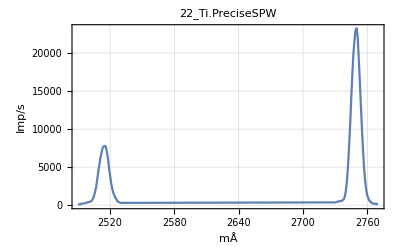

```mathematica
Render["22_Ti.PreciseSPW.txt"]
```

```mathematica
SetDirectory["/Users/alex/Library/Mobile Documents/com~apple~CloudDocs/Лабы/Labs/Phys_Labs/5_sem/Lab524/PhysLab5"];
Sources=FileNames[];
Graphs={};
For[i=1,i≤Length[Sources],i++,
If[FileExtension[Sources[[i]]]=="txt",
SetDirectory["/Users/alex/Library/Mobile Documents/com~apple~CloudDocs/Лабы/Labs/Phys_Labs/5_sem/Lab524/PhysLab5"];
Export[StringJoin[StringReplace[Sources[[i]],".txt"-> ""],".pdf"],Render[Sources[[i]]]]
]
]
```

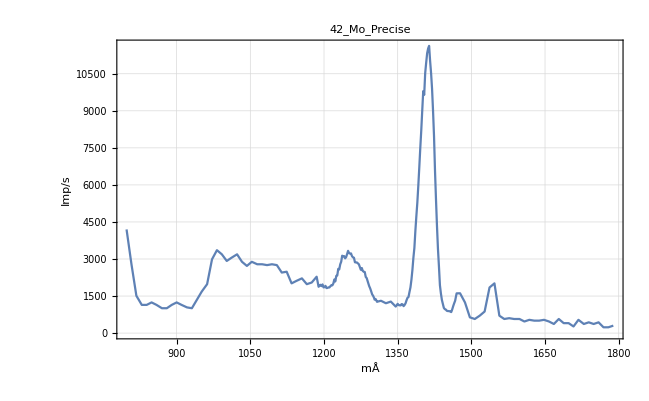

```mathematica
Render["42_Mo_Precise.txt"]
```

```mathematica
UnitConvert[Quantity[150,"Electronvolts"],"Ergs"]
```

2.403265×10^-10 ergs